```mathematica
sol = NDSolveValue[y'[x]+y[x] == x,y[x],x]
```

NDSolveValue::ndlim: Range specification x is not of the form {x, xend} or {x, xmin, xmax}.

NDSolveValue::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (1).

NDSolveValue[y[x]+y'[x]==x,y[x],x]

```mathematica
DSolveValue[{y'[x]+y[x] == x, y[0]==0},y[x],{x, -5, 5}]
```

-1+ⅇ^-x+x

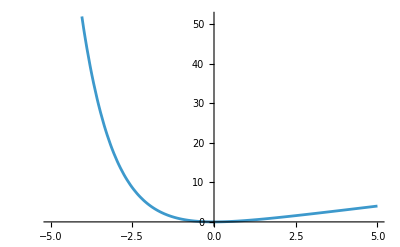

```mathematica
Plot[%, {x, -5,5}]
```

```mathematica
sol1= NDSolveValue[{y'[x]== Cos[x^2], y[0]==0},y[x],{x, -5, 5}]
```

InterpolatingFunction[…][x]

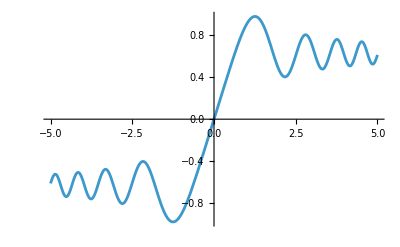

```mathematica
Plot[sol1, {x, -5,5}]
```

```mathematica
sol2 = NDSolveValue[{y'[x]== Sin[5*x]/(1+x*x), y[0]==0},y[x],{x, -50, 50}]
```

InterpolatingFunction[…][x]

```mathematica
Plot[sol2, {x, -50,50}]
```

```mathematica
sol5 = NDSolveValue[{y''[x]== 99 - y[x]^3, y'[0]==0, y[Pi/2]==0},y'[x],{x, 0, Pi/2}]
```

InterpolatingFunction[…][x]

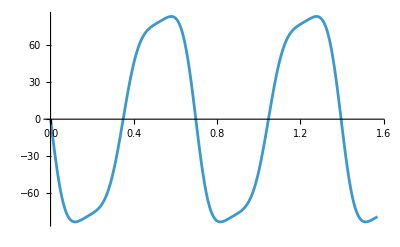

```mathematica
Plot[sol5, {x, 0, Pi/2}]
```